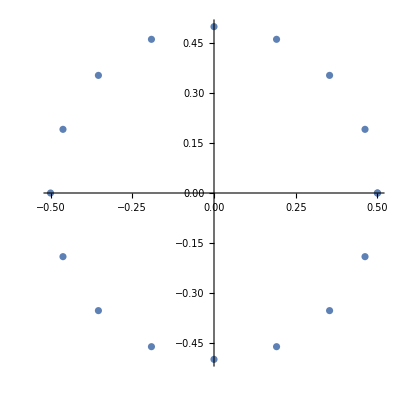

{{0.5,0.},{0.46,0.19},{0.35,0.35},{0.19,0.46},{0.,0.5},{-0.19,0.46},{-0.35,0.35},{-0.46,0.19},{-0.5,0.},{-0.46,-0.19},{-0.35,-0.35},{-0.19,-0.46},{0.,-0.5},{0.19,-0.46},{0.35,-0.35},{0.46,-0.19},{0.5,0.}}

```mathematica
r = 0.5;
t = N[Range[0,2.*Pi,Pi/8]];
x = r * Cos[t];
y = r * Sin[t];
(*ListPlot[{x,y}]*)
data = Transpose[{x,y}];
ListPlot[data, AspectRatio -> 1]
Round[data,0.01]
```

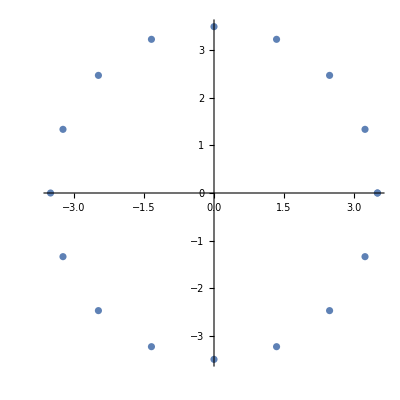

{{3.5,0.},{3.23,1.34},{2.47,2.47},{1.34,3.23},{0.,3.5},{-1.34,3.23},{-2.47,2.47},{-3.23,1.34},{-3.5,0.},{-3.23,-1.34},{-2.47,-2.47},{-1.34,-3.23},{0.,-3.5},{1.34,-3.23},{2.47,-2.47},{3.23,-1.34},{3.5,0.}}

```mathematica
rgauss = 3.5;
t = N[Range[0,2.*Pi,Pi/8]];
xgauss = rgauss * Cos[t];
ygauss = rgauss * Sin[t];
(*ListPlot[{x,y}]*)
datagauss = Transpose[{xgauss,ygauss}];
ListPlot[datagauss, AspectRatio->1]
Round[datagauss,0.01]
```

```mathematica
slope = {0.0007826239771925043,0.0009039493509247832,0.0010428497650549662} * 10.
intercept = {-0.003527443175143303,-0.008846942705030204,-0.009250214551616835} *10.
```

{0.00782624,0.00903949,0.0104285}

{-0.0352744,-0.0884694,-0.0925021}

### x - y

{451.721,417.679,320.735,175.648,4.5072,-166.634,-311.72,-408.664,-442.706,-408.664,-311.72,-166.634,4.5072,175.648,320.735,417.679,451.721}

{9.78699,157.958,283.572,367.504,396.977,367.504,283.572,157.958,9.78699,-138.384,-263.998,-347.93,-377.403,-347.93,-263.998,-138.384,9.78699}

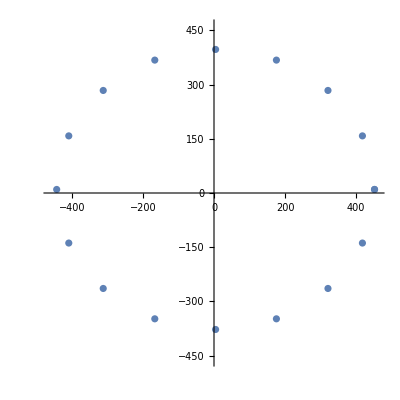

```mathematica
currentx = (xgauss - intercept[[1]])/slope[[1]]
currenty = (ygauss - intercept[[2]])/slope[[2]]
dataxy = Transpose[{currentx,currenty}];
ListPlot[dataxy,PlotRange->{{-460,460},{-460,460}}, AspectRatio->1]
Round[dataxy,0.01]
```

```mathematica
{{451.72,9.79},{417.68,157.96},{320.73,283.57},{175.65,367.5},{4.51,396.98},
{-166.63,367.50},{-311.72,283.57},{-408.66,157.96},{-442.71,9.79},
{-408.66,-138.38},{-311.72,-264.00},{-166.63,-347.93},
{4.51,-377.40},{175.65,-347.93},{320.73,-264.},{417.68,-138.38},
{451.72,9.79}}
```

### x - z

{451.721,417.679,320.735,175.648,4.5072,-166.634,-311.72,-408.664,-442.706,-408.664,-311.72,-166.634,4.5072,175.648,320.735,417.679,451.721}

{8.87013,137.306,246.188,318.941,344.489,318.941,246.188,137.306,8.87013,-119.566,-228.448,-301.201,-326.749,-301.201,-228.448,-119.566,8.87013}

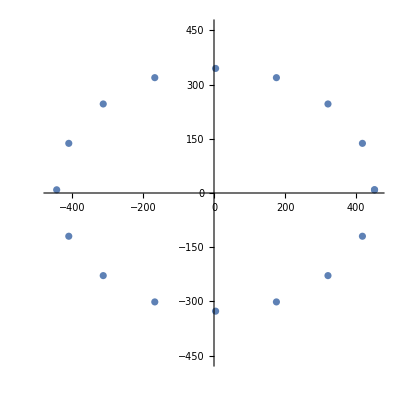

```mathematica
currentx = (xgauss - intercept[[1]])/slope[[1]]
currentz = (ygauss - intercept[[3]])/slope[[3]]
dataxz = Transpose[{currentx,currentz}];
ListPlot[dataxz,PlotRange->{{-460,460},{-460,460}}, AspectRatio->1]
Round[dataxz,0.01]
```

```mathematica
{{451.72,8.87},{417.68,137.31},{320.73,246.19},{175.65,318.94},{4.51,344.49},{-166.63,318.94},{-311.72,246.19},{-408.66,137.31},{-442.71,8.87},{-408.66,-119.57},{-311.72,-228.45},{-166.63,-301.2},{4.51,-326.75},
{175.65,-301.2},{320.73,-228.45},{417.68,-119.57},{451.72,8.87}}
```

### y - z

{396.977,367.504,283.572,157.958,9.78699,-138.384,-263.998,-347.93,-377.403,-347.93,-263.998,-138.384,9.78699,157.958,283.572,367.504,396.977}

{8.87013,137.306,246.188,318.941,344.489,318.941,246.188,137.306,8.87013,-119.566,-228.448,-301.201,-326.749,-301.201,-228.448,-119.566,8.87013}

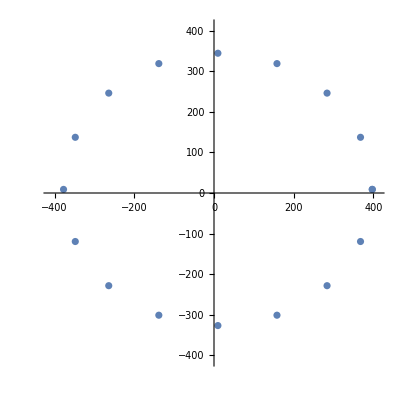

{{396.98,8.87},{367.5,137.31},{283.57,246.19},{157.96,318.94},{9.79,344.49},{-138.38,318.94},{-264.,246.19},{-347.93,137.31},{-377.4,8.87},{-347.93,-119.57},{-264.,-228.45},{-138.38,-301.2},{9.79,-326.75},{157.96,-301.2},{283.57,-228.45},{367.5,-119.57},{396.98,8.87}}

```mathematica
currenty = (xgauss - intercept[[2]])/slope[[2]]
currentz = (ygauss - intercept[[3]])/slope[[3]]
datayz = Transpose[{currenty,currentz}];
ListPlot[datayz,PlotRange->{{-410,410},{-410,410}}, AspectRatio->1]
Round[datayz,0.01]
```